```mathematica
Clear["Global`*"]
Off[DeleteDirectory::nodir]
(*Required Package*)
Needs["ErrorBarPlots`"]
(*Required Folder*)
SetDirectory[NotebookDirectory[]]
DeleteDirectory["Resultsum",DeleteContents->True];
CreateDirectory["Resultsum"];
(*Dataset Folder Path*)
dataPath="/home/edwin/Dropbox/Cinvestav Experiments/Project/Results/down/2*/seq*/reParticula*.dat";
```

/home/edwin/Dropbox/Cinvestav Experiments/Project/Computational/Modules

#### Calibration

```mathematica
(*z Steps in μm*)
zStep=0.5;
(*Px to μm*)
Px=0.127735(*μm*);
(*Carvajal Parameters*)
α1=30.8437 (*Px*);
α2=1/145.2783 (*μm^-1*);
α3=-31.0573(*Px*);
```

```mathematica
(*Number of Particles*)
nFile=Length@FileNames[dataPath];
```

```mathematica
(*Import Data*)
data=Table[Import[FileNames[dataPath][[i]],"Data"],{i,nFile}];
```

```mathematica
(*Radius List*)
RListRaw=Table[Last/@data[[i]],{i,nFile}];
RList=Table[
aux=RListRaw[[i]];θ=1;
While[
RListRaw[[i,θ]]==0.,
aux=Drop[aux,1];θ++];
aux,
{i,nFile}];
```

```mathematica
(*Match Dataset Lengths*)
Lengths=Table[Length@RList[[i]],{i,nFile}];
RList=Px Map[Take[#,Min@Lengths]&,RList];
zList=Range[0.5,Min@Lengths zStep,zStep];
```

```mathematica
(*Calibration*)
zRList=Table[DeleteCases[Transpose[{zList,RList[[i]]}],{_,0.}],{i,nFile}];
```

```mathematica
(*Calibration Fits*)
zRFits=Table[LinearModelFit[zRList[[i]],{x},x],{i,nFile}];
RMeanList=Mean/@Transpose[Table[Table[zRFits[[j]][zList[[i]]],{i,Length@zList}],{j,nFile}]];
σMeanList=StandardDeviation/@Transpose[Table[Table[zRFits[[j]][zList[[i]]],{i,Length@zList}],{j,nFile}]];
zRMeanList=Transpose[{zList,RMeanList}];
zRFit=LinearModelFit[zRMeanList,{x},x,Weights->1/σMeanList^2];
```

```mathematica
(*Degrees of Freedom*)
ν=zRFit["ANOVATableDegreesOfFreedom"][[2]];
(*Reduced χ^2*)
χ2ν=Total[zRFit["StandardizedResiduals"]^2]/ν;
(*Probability*)
P=SurvivalFunction[ChiSquareDistribution[ν],χ2ν ν];
(*Autocorrelation Test*)
d=Total[Differences[zRFit["StandardizedResiduals"]]^2]/Total[zRFit["StandardizedResiduals"]^2];
```

#### Print Results

Statistical Parameters

R^2 = 1.

ν = 16.

χ_ν^2 = 1.103

P(χ_ν^2;ν) = 0.3449

D = 0.929

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.719703 | 4.48668×10^-16 | 1.60409×10^15 | 4.38939×10^-235
x | 0.4683 | 1.03293×10^-16 | 4.53372×10^15 | 2.64721×10^-242

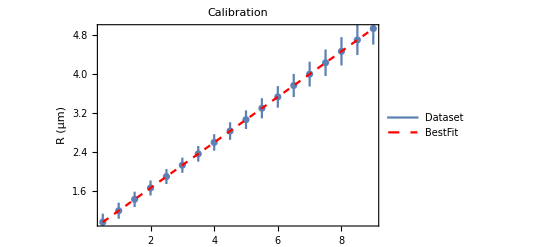

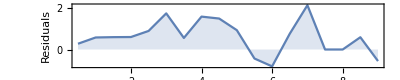

```mathematica
(*Print Results*)
Print[]
Print[Style["Statistical Parameters",Underlined]]
Print["R^2 = ", SetPrecision[zRFit["RSquared"],4]]
Print["ν = ", SetPrecision[ν,4]]
Print["χ_ν^2 = ", SetPrecision[χ2ν,4]]
Print["P(χ_ν^2;ν) = ", SetPrecision[P,4]]
Print["D = ", SetPrecision[d,4]]
Print[zRFit["ParameterTable"]]
Print[]
(*Fit Plot*)
zRMeanListσ=MapAt[ErrorBar,Transpose[{zRMeanList,σMeanList}],{All,2}];
plot=Legended[Show[
ErrorListPlot[zRMeanListσ],
Plot[zRFit[x],{x,First@zList,Last@zList},PlotStyle->{Red,Dashed}],
Frame->True,
FrameLabel->{None,"R (μm)"},
PlotLabel->"Calibration",
PlotRange->{{Min[First/@zRMeanList],Max[First/@zRMeanList]},{Min@DeleteCases[RMeanList,0.],Max@RMeanList}}],
Placed[LineLegend[{ColorData[97][1],{Red,Dashed}},{"Dataset","BestFit"},LegendFunction->Panel],{{0.05,0.7},{0,0}}]]
(*Residuals Plot*)
ResPlot=ListLinePlot[Transpose[{First/@zRMeanList,zRFit["StandardizedResiduals"]}], 
AspectRatio->1/5,
Frame->True,
Filling->Axis,
FrameLabel->{"z (μm)","Residuals"},
PlotRange->{{Min[First/@zRMeanList],Max[First/@zRMeanList]},Automatic}]
```

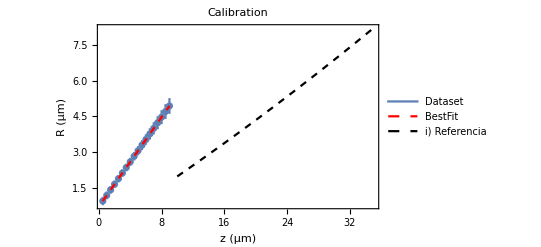

```mathematica
plotCombined=Legended[Show[
ErrorListPlot[zRMeanListσ],
Plot[zRFit[x],{x,First@zList,Last@zList},PlotStyle->{Red,Dashed}],
Plot[α1 Exp[α2 x]+α3,{x,10,35},PlotStyle->{Dashed,Black}],
Frame->True,
FrameLabel->{"z (μm)","R (μm)"},
PlotLabel->"Calibration",
PlotRange->{{0.5,35},Automatic}],
Placed[LineLegend[{ColorData[97][1],{Red,Dashed},{Black,Dashed}},{"Dataset","BestFit","i) Referencia"},LegendFunction->Panel],{{0.58,0.7},{0.,1.8}}]]
```

```mathematica
(*Export Numerical Results & Plots*)
Export["Resultsum/CalibrationPlot.pdf",plot];
Export["Resultsum/Residuals.pdf",ResPlot];
Export["Resultsum/CombinedPlot.pdf",plotCombined];
Export["Resultsum/R2.dat",SetPrecision[zRFit["RSquared"],4]];Export["Resultsum/DoF.dat",SetPrecision[ν,4]];Export["Resultsum/Chi2.dat",SetPrecision[χ2ν,4]];Export["Resultsum/P.dat",SetPrecision[P,4]];
Export["Resultsum/D.dat",SetPrecision[d,4]];
Export["Resultsum/b.dat",SetPrecision[zRFit["BestFitParameters"][[1]],4]];
Export["Resultsum/m.dat",SetPrecision[zRFit["BestFitParameters"][[2]],4]];
Export["Resultsum/muRes.dat",SetPrecision[Mean@zRFit["StandardizedResiduals"],2]];
Export["Resultsum/sigmaRes.dat",SetPrecision[StandardDeviation@zRFit["StandardizedResiduals"],2]];
```